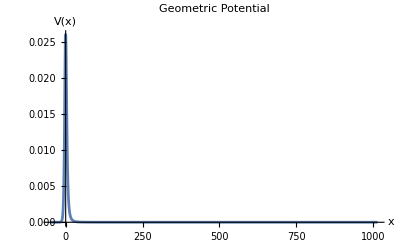

Γ_(0,0)

{{0.01,0.00171226},{0.02,0.00739614},{0.03,0.0180538},{0.04,0.034894},{0.05,0.0592528},{0.06,0.0924445},{0.07,0.135525},{0.08,0.18898},{0.09,0.252398},{0.1,0.324246},{0.11,0.401878},{0.12,0.481846},{0.13,0.560456},{0.14,0.634389},{0.15,0.701192},{0.16,0.759457},{0.17,0.808778},{0.18,0.849519},{0.19,0.882512},{0.2,0.908827},{0.21,0.929562},{0.22,0.945755},{0.23,0.958319},{0.24,0.968017},{0.25,0.975491},{0.26,0.981209},{0.27,0.985603},{0.28,0.988972},{0.29,0.991541},{0.3,0.993518},{0.31,0.995019},{0.32,0.996176},{0.33,0.997058},{0.34,0.997736},{0.35,0.998253},{0.36,0.998652},{0.37,0.998965},{0.38,0.99919},{0.39,0.999372},{0.4,0.999507},{0.41,0.999624},{0.42,0.999696},{0.43,0.999764},{0.44,0.999815},{0.45,0.999838},{0.46,0.999874},{0.47,0.999893},{0.48,0.999908},{0.49,0.999921},{0.5,0.999934},{0.51,0.999937},{0.52,0.999936},{0.53,0.999943},{0.54,0.99995},{0.55,0.999952},{0.56,0.999953},{0.57,0.999954},{0.58,0.999954},{0.59,0.999952},{0.6,0.999955},{0.61,1.00001},{0.62,0.999948},{0.63,0.999952},{0.64,0.999974},{0.65,0.999956},{0.66,0.999955},{0.67,0.999951},{0.68,0.999954},{0.69,0.999949},{0.7,1.00002},{0.71,0.999953},{0.72,0.999958},{0.73,1.00002},{0.74,0.999942},{0.75,0.999943},{0.76,0.999945},{0.77,0.999962},{0.78,0.999946},{0.79,0.999952},{0.8,0.999946},{0.81,0.999944},{0.82,0.999947},{0.83,1.00002},{0.84,0.999944},{0.85,1.00002},{0.86,0.99995},{0.87,0.999944},{0.88,0.999941},{0.89,0.999931},{0.9,0.999947},{0.91,0.99993},{0.92,0.999943},{0.93,0.999946},{0.94,1.00003},{0.95,0.999933},{0.96,0.999916},{0.97,0.999932},{0.98,0.999943},{0.99,0.999937},{1.,0.999946}}

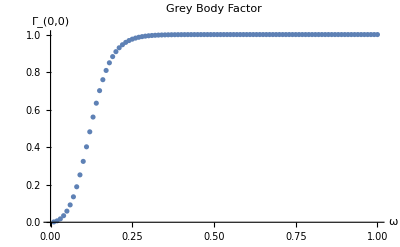

```mathematica
(**    GrayHawk    **)


(*
The program consists of a single, self-contained piece of code that can be executed with a single command. Upon execution,the tool generates several outputs, including:a plot of the geometric potential,a table displaying the computed GBF values,and a corresponding GBF plot. The following units are adopted in the code
c=G=ℏ=1
*)

Clear["Global`*"]

(*Parameters*)

(*
In this section, the code is initialized with the explicit values of the parameters defining both the field and the metric,as well as the energy values at which the GBFs are to be evaluated. It is important to note that the mass parameter M must be set to one, as the code is designed to operate in units normalized to the black hole mass.
*)

(*BH parameters*)

(*
This subsection is dedicated to specifying the parameters that define the metric. If a user wishes to implement a metric other than the pre-compiled options, any additional parameter(s) associated with the new metric must be specified in this section.
*)

M=1; (*Mass of the black hole set to unity*)
Q=0; (*Charge of the BH*)
ℓ=0;(*Regularizing Parameters*)

(*Field parameters*)

(*
In this section,users can specify the spin of the field for which the GBF is to be calculated, as well as the field mode in the spherical harmonic
decomposition.
*)

s=0; (*Field spin*)
l=0; (*Mode multipole number, l>=s*)


(*Energy table*)

(*
It is defined here the table of energies at which the GBF have to be probed.
*)

ωj=Table[0.01 j ,{j,1,100}];(*Table of energies where to evaluete the GBF*)



(*The metric*)

(*
A set of pre-compiled metrics is provided for user convenience. To utilize these pre-compiled metrics,the user simply needs to uncomment the desired metric consistently
across the three metric functions (F (r), G(r), and H(r)). If the user wishes to implement a custom line element that is not pre-compiled, it can be introduced in this section. However, it is important to note that altering the line element does not guarantee accurate results. Any newly introduced line element must represent an asymptotically
flat black hole. We will take into account a metric in the form ds^2= -G(r)dt^2 + F(r)^-1 dr^2 + H(r)dΩ^2 where dΩ^2=dθ^2+ Sin[θ]^2 dϕ^2.
*)

(*Definition of F(r)*)

F[r_]:=Simplify[
(*Schwarzschild*)1-(2 M)/r
(*Reissner-Nordstrom*)(*1-(2 M)/r+Q^2/r^2*)
(*Hayward*)(*1-(2 M r^2)/(r^3+2 M ℓ^2)*)
(*Bardeen*)(*1-(2 M r^2)/((r^2+ℓ^2)^(3/2))*)
(*Simpson-Visser*)(*1-(2 M)/(√(r^2+ℓ^2))*)
(*Peltola-Kunstatter*)(*(r-2 M)/(√(r^2+ℓ^2))*)
(*D’Ambrosio-Rovelli*)(*(1-(2 M)/(√(r^2+ℓ^2)))/(1+ℓ/(√(r^2+ℓ^2)))*)
,{r>=0,ℓ>=0}];

(*Definition of G(r)*)

G[r_]:=Simplify[
(*Schwarzschild*)1-(2 M)/r
(*Reissner-Nordstrom*)(*1-(2 M)/r+Q^2/r^2*)
(*Hatward*)(*1-(2 M r^2)/(r^3+2 M ℓ^2)*)
(*Bardeen*)(*1-(2 M r^2)/((r^2+ℓ^2)^(3/2))*)
(*Simpson-Visser*)(*1-(2 M)/(√(r^2+ℓ^2))*)
(*Peltola-Kunstatter*)(*(r-2 M)/(√(r^2+ℓ^2))*)
(*D’Ambrosio-Rovelli*)(*(1-(2 M)/(√(r^2+ℓ^2)))*)
,{r>=0,ℓ>=0}];

(*Definition of H(r)*)

H[r_]:=Simplify[
(*tr-Symmetric*)r^2
(*non-tr-Symmetric/Black-Bounces*)(*r^2+ℓ^2*),{r>=0,ℓ>=0}];




(*Numerical inversion of tortoise coordinates*)

(*
To explicitly express (∂_(r^*))^2 Z(r^*) +((ω^2-Subscript[V, eff](r^*))) Z(r^*)=0, it is necessary to determine Subscript[V, eff](r^*) and, consequently, r(r^*). In this section, we implement a
numerical procedure that generates a table of r values as a function of r^*. This table is subsequently interpolated to obtain a continuous representation of r(r^*). In order not to create misinterpretation of the tortoise coordinate, we rename it as "x" through out the rest of the code.
*)


 (*Definition of the horizon radius*)

(*
The horizon radius rH is obtained as the largest root of F(r).
*)

rH=Max[r/.Solve[F[r]==0]];

(*Definition of the tortoise coordinate*)

(*
The tortoise coordinate x is obtained by integrating √(1/(F(r) G(r))) utilizing Mathematica’s builtin Integrate[] function and computing the indefinite integral of √(1/(F(r) G(r))). However, modifying the metric may lead to complications with this procedure since Integrate[√(1/(F(r) G(r)))] may not yield an explicit analytic result. In such cases, a purely numerical integration approach may need to be employed.
*)

x[r_]=Re[Integrate[√(1/(F[r] G[r])),r]]; 

(*Numerical inversion*)

(*
The sampling of x(r) is divided into two distinct regimes: one near the horizon and another in the far-away region. It is crucial that these
two regimes overlap in the central region, ensuring continuity when combined. The sampling criteria are flexible and depend on the user-defined parameters specified
in the first section. Users are advised to verify the efficiency of the sampling using the CalibratorGH.nb tool to ensure compatibility with their chosen energy and
parameter values. The two sampling regimes are subsequently merged and interpolated within the boundaries of the sampled region.
*)

(*Near-Horizon sampling*)

nbrr=1000;
tr=N[rH(1+10^Range[-11,-1,(10/(nbrr-1))])];
For[i=1,i<nbrr,i++,X[i]={x[tr[[i]]],tr[[i]]};];
X1=Table[X[nbrr-i],{i,1,nbrr-2}];

(*Far-Horizon sampling*)

For[i=2,i<5000,i++,
X[i]={x[rH(1+0.1i)],rH(1+0.1i)};
]
X2=Table [X[i],{i,2,4999}];


(*Inverted tortoise coordinates*)

XX=Join[X1,X2];(*Inverted tortoise table*)

xmin∞=Min[XX];(*Minimum value of the tortoise coordinate according to the sampling (maximum close to horizon distance according to the sampling)*)
xmax∞=Max[XX];(*Maximum value of the tortoise coordinate according to the sampling (maximum far to horizon distanceaccording to the sampling)*)

r=Interpolation[XX]; (*Inverted tortoise function*)


(*The geometrical potential*)

(*
In this section, we utilize the definition of Subscript[V, eff](x) along with the results obtained from the previous section to explicitly compute Subscript[V, eff](x). Additionally, this section includes a plot of the geometric potential, which serves as a diagnostic tool to verify whether the potential vanishes at the boundaries
of the region of interest. If the potential does not approach zero at the boundaries, adjustments to the sampling described in the previous section may be required.
*)

(*Auxiliary functions*)

DDSqrtH=D[D[√H[r[x]],x],x];
DH=D[H[r[x]],x];
DSqrtGoverH=D[√(G[r[x]]/H[r[x]]),x];
ν=l(l+1)-s(s-1); (*Separation constant*)


(*Geometric potential definition*)

Veff[x_]:=If[s==0,G[r[x]]/H[r[x]] ν+DDSqrtH/(√H[r[x]]),
		If[s==2,G[r[x]]/H[r[x]] ν+(DH)^2/(2 H[r[x]]^2)-DDSqrtH/(√H[r[x]]),
		If[s==1,G[r[x]]/H[r[x]] ν,
		If[s==1/2,G[r[x]]/H[r[x]] ν + √ν DSqrtGoverH]]]];

(*Geometric Potential Plot*)

Plot[Veff[x],{x,xmin∞,xmax∞},PlotRange->All,PlotLabel->"Geometric Potential",AxesLabel->{"x","V(x)"}](*ACHTUNG: make sure that the potential is vanishing both near the orizon and in the far away region*)


(*Solving for the GBF*)

(*
This section implements the core part of the calculation, focusing on the table of energies at which the GBF is to be evaluated. A for loop is employed to
solve the scattering problem for each energy listed in the table. The procedure for solving the scattering problem is as follows:
         - Equation  (∂_x)^2 Z(x) +((ω^2-Subscript[V, eff](x))) Z(x)=0 is solved by imposing purely ingoing boundary conditions and normalizing the wave function at the event horizon.
    - A region in the asymptotic far-away domain is defined.
    - In that region the computed solution is sampled and fitted using the asymptotic expression valid for x -> ∞: Z(x)≈ 𝒶 e^iωx + 𝒷 e^iωx.
- The GBF is computed as Γ=|𝒷|^-2, where b is obtained from the far-field fit.

At the conclusion of the for loop,the calculated values of Γ are compiled into a displayed table and subsequently plotted for visualization
*)


	For[j=1,j<=Length[ωj],j++,	

	
		ω=ωj[[j]]; (*Frequency of the incoming wave*)

		(*Define the Schrödinger-like equation*)
		schrodingerEq=D[Z[x],{x,2}]+(ω^2-Veff[x]) Z[x]==0;

		(*Boundary conditions for the wavefunction near the horizon*)
		boundaryConditions={Z[xmin∞]==Exp[-I ω (xmin∞)],Z'[xmin∞]==(-I ω)Exp[-I ω (xmin∞)]};

		(*Solve the equation numerically*)
		sol=NDSolve[{schrodingerEq,boundaryConditions},Z,{x,xmin∞,xmax∞}];
	

					(*Far horizon region reconstruction (integration out)*)

					xfar=IntegerPart[xmax∞/4];(*Distance from xmax∞ such that xmax∞-xfar is still in the far region*)

					(*Sampling in the far horizon region*)

							For[
								i=0,i<=xfar,i++,
								p[i]=Z[xmax∞-xfar+i]/. sol
		
								];

					FF=Flatten[Table[p[i],{i,0,xfar}]];(*Table of values of the solution*)
					NLM=NonlinearModelFit[FF,𝒶 Exp[I ω x]+𝒷 Exp[- I ω x],{𝒶,𝒷},x]; (*Fit of the solution *)
					T[j]=1/(Abs[𝒷 /.NLM["BestFitParameters"]])^2(*GBF value at ωj*)
			]

Print[Subscript["Γ", s,l]]
Γ=Table[{ωj[[ j]],T[j]},{j,1,Length[ωj]}] (*GBF table*)

(*GBF Plot*)
ListPlot[Γ,PlotRange->All,PlotLabel->"Grey Body Factor",AxesLabel->{"ω",Subscript["Γ", s,l]}]
```